```mathematica
SetDirectory["C:\\Users\\Georg\\Desktop\\figs"];
<<"CustomTicks.m"
```

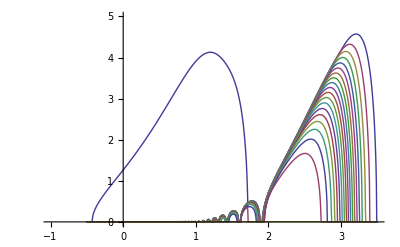

```mathematica
a=.
n=20;
z=1/n;
ϵ=1/2;
λ=0.;
μ=10^a;
h=-1;
ω=Table[-1,{i,1,n}]~Join~Table[+1,{i,1,n}];
g=Table[h μ,{i,1,n}]~Join~Table[-h (1+ϵ) μ,{i,1,n}]/n;
u=.
uu=Table[(1-n z)/2+z(i-1/2),{i,1,n}]~Join~Table[(1-n z)/2+z(i-1/2),{i,n,1,-1}];
m=Table[KroneckerDelta[i,j] (ω[[i]]+(ϵ μ+λ) uu[[i]])-(uu[[i]]+uu[[j]]) g[[j]],{i,1,2 n},{j,1,2 n}];
pmax=n;
MySort[m_]:=Module[{s},s=Sort[Im[Eigenvalues[m]],Greater];Table[s[[i]],{i,1,pmax}]]
kap=Table[{a}~Join~MySort[m],{a,-0.5,3.5,0.005}];
len=Length[kap];
ListLinePlot[Table[Table[{kap[[i,1]],kap[[i,1+j]]},{i,1,len}],{j,1,pmax}],PlotRange->{{-1,3.5},{0,5}}]
```

```mathematica
n=20;
z=1/n;
ϵ=1/2;
λ=0.;
μ=.
h=-1;
ω=Table[-1,{i,1,n}]~Join~Table[+1,{i,1,n}];
g=Table[h μ,{i,1,n}]~Join~Table[-h (1+ϵ) μ,{i,1,n}]/n;
u=.
uu=Table[(1-n z)/2+z(i-1/2),{i,1,n}]~Join~Table[(1-n z)/2+z(i-1/2),{i,n,1,-1}];
m=Table[KroneckerDelta[i,j] (ω[[i]]+(ϵ μ+λ) uu[[i]])-(uu[[i]]+uu[[j]]) g[[j]],{i,1,2 n},{j,1,2 n}];
pmax=n;
MySort[m_]:=Module[{s},s=Sort[Im[Eigenvalues[m]],Greater];Table[s[[i]],{i,1,pmax}]]
```

```mathematica
μ=1000.;
MySort[m]
```

{4.17783,4.16633,4.09715,3.99494,3.86644,3.71288,3.53254,3.32109,3.07093,2.76905,2.39141,1.88484,1.05987,0,0,0,0,0,0,0}

```mathematica
Eigenvalues[m]
Ω1=Part[Eigenvalues[m],7]
```

{484.337+4.17783 ⅈ,484.337-4.17783 ⅈ,458.729+4.16633 ⅈ,458.729-4.16633 ⅈ,433.287+4.09715 ⅈ,433.287-4.09715 ⅈ,407.92+3.99494 ⅈ,407.92-3.99494 ⅈ,382.595+3.86644 ⅈ,382.595-3.86644 ⅈ,357.297+3.71288 ⅈ,357.297-3.71288 ⅈ,332.017+3.53254 ⅈ,332.017-3.53254 ⅈ,306.747+3.32109 ⅈ,306.747-3.32109 ⅈ,281.485+3.07093 ⅈ,281.485-3.07093 ⅈ,256.225+2.76905 ⅈ,256.225-2.76905 ⅈ,-244.946,230.965+2.39141 ⅈ,230.965-2.39141 ⅈ,205.701+1.88484 ⅈ,205.701-1.88484 ⅈ,180.43+1.05987 ⅈ,180.43-1.05987 ⅈ,156.425,153.867,132.041,127.645,107.448,101.574,82.7839,75.4778,58.0988,49.2269,33.4395,22.5164,8.93406}

407.92+3.99494 ⅈ

```mathematica
n=20;
ϵ=1/2;
μ=1000.;
Ω=Ω1;
h=-1;
i0=Sum[(-μ/(-1+ϵ μ ((i-1/2)/n) -Ω)+μ(1+ϵ)/(1+ϵ μ ((i-1/2)/n)-Ω))/n,{i,1,n}]
i1=Sum[((i-1/2)/n)(-μ/(-1+ϵ μ ((i-1/2)/n)-Ω)+μ(1+ϵ)/(1+ϵ μ ((i-1/2)/n)-Ω))/n,{i,1,n}]
i2=Sum[((i-1/2)/n)^2(-μ/(-1+ϵ μ ((i-1/2)/n)-Ω)+μ(1+ϵ)/(1+ϵ μ ((i-1/2)/n)-Ω))/n,{i,1,n}]
(h+i1)^2-i0 i2//FullSimplify
```

-0.000697972+0.000453494 ⅈ

0.990156-0.0312743 ⅈ

1.29075-0.0434897 ⅈ

-1.67257×10^-13+2.87129×10^-13 ⅈ

```mathematica
b=1;
a=Last[Last[Last[Solve[(i1-h)aa+i2 b==0,aa]]]];
ω=0;
Q[ω_,u_]:=(a+b u)/(ω+(ϵ μ+λ)u-Ω)
ω=0;
rx=.
ry=.
eq1=(Re[Q[ω,0]]-rx)^2+(Im[Q[ω,0]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
eq2=(Re[Q[ω,1]]-rx)^2+(Im[Q[ω,1]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
ss=Solve[{eq1,eq2},{rx, ry}];
rx=Last[First[Last[ss]]];
ry=Last[Last[Last[ss]]];
p=(rx - I ry)/(rx^2+ry^2);
ω=.
Clear[Q]
Q[ω_,u_]:=p(a+b u)/(ω+(ϵ μ+λ)u-Ω)
Q[ω,u]//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-((1.04914+47.7947 ⅈ) ((-0.64875+0.0116577 ⅈ)+u))/((-407.92-3.99494 ⅈ)+500. u+ω)

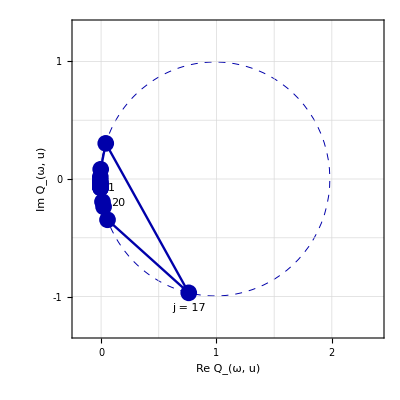

disvec1.eps

```mathematica
p1=ParametricPlot[{{Re[Q[1,u]],Im[Q[1,u]]}},{u,0,1},PlotRange->{{-0.2,2.4},{-1.3,1.3}},AspectRatio->1,
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},
PlotStyle->{{AbsoluteThickness[0.7],Darker[Blue],Dashed},{AbsoluteThickness[0.7],Darker[Red],Dashed},{AbsoluteThickness[0.5],Black}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,GridLines->{{0,0.5,1,1.5,2},{-1,-0.5,0,0.5,1}},
Epilog-> {Inset["j = 17",{0.76,-1.1},{Center,Center}],Inset["1",{0.09,-0.08},{Center,Center}],Inset["20",{0.15,-0.20},{Center,Center}]},
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["Re Q_(ω, u)",14],Style["Im Q_(ω, u)",14]},
FrameTicks->{LinTicks[-1,3,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-1,3,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[-2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}];
v1=Table[{Re[Q[1,uu[[i]]]],Im[Q[1,uu[[i]]]]},{i,1,20}];
v2=Table[{Re[Q[-1,uu[[i]]]],Im[Q[-1,uu[[i]]]]},{i,21,40}];
p2=ListPlot[{v1},Axes->False,
PlotStyle->{{PointSize[0.03],Darker[Blue]}}];
p3=ListLinePlot[{v1},PlotStyle->{{AbsoluteThickness[1.7],Darker[Blue]}},PlotRange->All,Axes->False];
plot1=Show[p1,p2,p3]
Export["disvec1.eps",plot1]
```